```mathematica
text = Import["C:\\Documents and Settings\\Administrator\\桌面\\douban\\book_detail.txt",CharacterEncoding->"CP936"];
text = StringSplit[text,"\n"];
{bookname,id,rate,ratenum}=text⟦#;;;;8⟧&/@{1,2,3,4};
```

```mathematica
id = StringCases[#,DigitCharacter..]⟦1⟧&/@id;
```

```mathematica
rate=StringCases[#,"\tRate:"~~(x:__):> ToExpression[x]]⟦1⟧&/@rate;
```

```mathematica
ratenum=ToExpression[StringCases[#,DigitCharacter..]⟦1⟧]&/@ratenum;
```

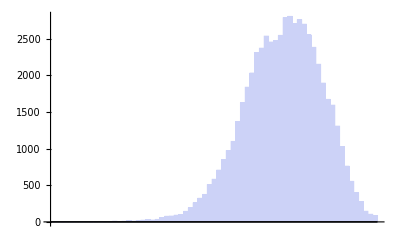

```mathematica
SortBy[Tally@rate,First];
BarChart[%⟦2;;,2⟧]
```

```mathematica
n = Length@bookname;
bestbook={bookname⟦#⟧,rate⟦#⟧,ratenum⟦#⟧}&/@Select[Range@n,rate⟦#⟧>9&&ratenum⟦#⟧>10000&];
SortBy[bestbook,#⟦2⟧&]//Reverse//Column
```

{灌篮高手（31）,9.5,25388}
{红楼梦,9.5,88089}
{海贼王,9.5,23581}
{史记,9.5,10742}
{机器猫哆啦A梦23,9.4,27123}
{1984,9.3,10890}
{1984,9.3,10076}
{冰与火之歌（卷一）,9.3,16767}
{撒哈拉的故事,9.3,12019}
{撒哈拉的故事,9.3,10855}
{撒哈拉的故事,9.3,10613}
{飘（上下）,9.3,61462}
{一九八四,9.3,17514}
{活着,9.3,13208}
{一九八四·动物农场,9.2,21619}
{七龍珠 34,9.2,21676}
{子不语3,9.2,11463}
{福尔摩斯探案全集（上中下）,9.2,42553}
{三国演义（全二册）,9.2,47330}
{撒哈拉的故事,9.2,32557}
{百年孤独,9.2,42867}
{动物农场,9.2,21107}
{小王子,9.2,10321}
{三体Ⅲ,9.2,38614}
{三体Ⅱ,9.2,37147}
{NANA（1-13）,9.1,15788}
{明朝那些事儿（1-9）,9.1,23841}
{子不语(1,2),9.1,14904}
{機器娃娃(1),9.1,10684}
{小王子（中英文对照本）,9.1,10163}
{平凡的世界（全三部）,9.1,70350}
{经济学原理（上下）,9.1,10032}
{天龙八部（全五册）,9.1,45739}
{安徒生童话故事集,9.1,31924}
{中国历代政治得失,9.1,16435}
{肖申克的救赎,9.1,28744}
{父与子全集,9.1,14587}
{动物庄园,9.1,11173}
{小王子,9.1,10024}
{活着,9.1,92948}
{活着,9.1,64119}
{围城,9.1,12139}